This notebook generate the figures in the supplementary Fig. 2 and Fig. 3.

```mathematica
saveDir=NotebookDirectory[];
```

## Gain media dynamics

```mathematica
{tx,ty,tz,ti} = PauliMatrix[#]&/@Range[4];
```

```mathematica
tp = 1/2(tx+ⅈ ty);
tm = 1/2(tx-ⅈ ty);
```

```mathematica
sTrunc =3;
sopRL =Table[{j,j+1}->√(1. (j)),{j,1,sTrunc}];
sop=SparseArray[sopRL,{ (sTrunc+1), (sTrunc+1)}];
isop = IdentityMatrix[Length[sop]];
```

```mathematica
tTrunc =2;
topRL =Table[{j,j+1}->√(1. (j)),{j,1,tTrunc}];
top=SparseArray[topRL,{ (tTrunc+1), (tTrunc+1)}];
itop = IdentityMatrix[Length[top]];
```

```mathematica
rhoMtx[t_]:=Table[ρ[i][j][t],{i,(sTrunc+1)(tTrunc+1)},{j,(sTrunc+1)(tTrunc+1)}]
```

```mathematica
ClearAll[ωs,ωt,g3,g2,Ωd,Δ,γ,k]
```

```mathematica
ωs = 7.2;
ωt = 7.0-0.3;
g3 = 0.05;
g2 = 0.05;
Ωd=2.0;
k=-0.3;
Δ=Abs[ωs-ωt];
γ=0.005;
```

```mathematica
((Ωd g2 g3)/(ωs-ωt-k))^2/γ
```

0.0078125

```mathematica
Expand[(x+y)^4]
```

x^4+4 x^3 y+6 x^2 y^2+4 x y^3+y^4

```mathematica
h0 = ωs KroneckerProduct[sopᵀ.sop,itop] + g3 KroneckerProduct[sopᵀ.sop.(sopᵀ+sop),itop]+ωt KroneckerProduct[isop,topᵀ.top]+k/6 KroneckerProduct[isop,MatrixPower[topᵀ,4]+4MatrixPower[topᵀ,3].top+6topᵀ.topᵀ.top.top+4topᵀ.MatrixPower[top,3]+MatrixPower[top,4]]+g2 KroneckerProduct[sop,topᵀ]+g2 KroneckerProduct[sopᵀ,top];
```

```mathematica
sxOp = KroneckerProduct[sop+sopᵀ,itop];
hd[t_]:=2 Ωd Cos[(ωs+ωt)t]sxOp;
```

```mathematica
sOp=KroneckerProduct[sop,itop];
sOpd=sOpᵀ;
sOpN=sOpᵀ.sOp;
```

```mathematica
sBasis=Table[
KroneckerProduct[
SparseArray[i->1.0,Length[sop]]
,itop]
,{i,Length[sop]}];
sBasis//Dimensions
```

{4,12,3}

```mathematica
rho0=SparseArray[{1,1}->1.0,Dimensions[sOp]];
```

```mathematica
resTemp=.
```

```mathematica
resTemp = NDSolve[{D[rhoMtx[t],t]==-ⅈ(h0+hd[t]).rhoMtx[t]+ⅈ rhoMtx[t].(h0+hd[t]) - γ/2.0(sOpN.rhoMtx[t]+rhoMtx[t].sOpN-2 sOp.rhoMtx[t].sOpd),rhoMtx[0]==Normal[rho0]},rhoMtx[t],{t,0,10000},PrecisionGoal->5,AccuracyGoal->5];
```

```mathematica
diagList3=Table[
Diagonal[Evaluate[(rhoMtx[t]/.resTemp[[1]])/.{t->ts}]]
,{ts,0,10000,10}];
```

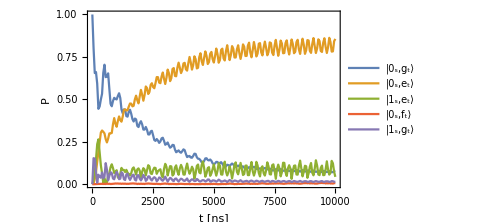

```mathematica
plt3=ListPlot[Transpose[{Range[0,10000,10],#}][[;;;;5]]&/@Transpose[Abs[diagList3]][[{1,2,5,3,4}]],PlotRange->Full,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"],FrameLabel->{"t [ns]","P"}
,Joined->True

,PlotLegends->(Style[#,16,FontFamily->"Times New Roman",Black]&/@{"|0_s,g_t⟩","|0_s,e_t⟩","|1_s,e_t⟩","|0_s,f_t⟩","|1_s,g_t⟩"})
,ImageSize->5 72]
```

```mathematica
rhot=Table[
rhoTemp=Evaluate[(rhoMtx[t]/.resTemp[[1]])/.{t->ts}];
Sum[sᵀ.rhoTemp.s,{s,sBasis}]
,{ts,0,10000,10}];
diagListT = Diagonal[#]&/@rhot;
```

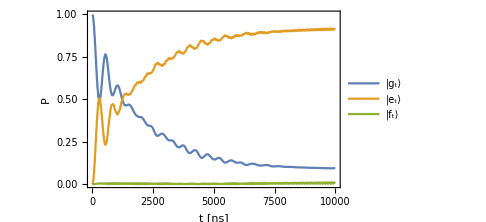

```mathematica
plt2=ListPlot[Transpose[{Range[0,10000,10],#}]&/@Transpose[Abs[diagListT]],PlotRange->Full,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"],FrameLabel->{"t [ns]","P"}
,Joined->True
,ImageSize->5 72
,PlotLegends->(Style[#,16,FontFamily->"Times New Roman",Black]&/@{"|g_t⟩","|e_t⟩","|f_t⟩"})]
```

## Eigenspectrum method justification

```mathematica
combineOps[op1_,op2_]:=Module[{top},
top = TensorProduct[op1,op2];
top = Flatten[Transpose[top,{1,3,4,2}],1];
top = Flatten[Transpose[top,{3,1,2}],1];
Return[topᵀ]
]
```

```mathematica
aTrunc = 110;
aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};
```

```mathematica
hac = aOp.sP + aOpᵀ.sM;
HacSO =-ⅈ ( combineOps[hac,iOp]-combineOps[iOp,hac]);


pumpSO = -1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);


normalLossSO = -1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);

lossSO = -1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
```

```mathematica
gammaC = 0.1;
lambdaA = 30;
gc=(√(gammaC lambdaA))/2
```

0.866025

```mathematica
superOp = 1.17 gc HacSO + lambdaA pumpSO + gammaC lossSO;
```

```mathematica
{eigVal,eigVect}=Eigensystem[superOp,-20];
```

```mathematica
steady= Partition[eigVect[[-1]],Length[aOp]];
steady=steady/Tr[steady];
```

```mathematica
record2={};
vec0 = Re[Flatten[aOp.steady]];

vecT = vec0;
tf=4000;
dt = 0.025;
step = Round[tf/dt];
Monitor[
Do[
k1=superOp.vecT;
k2 = superOp.(vecT+k1 dt);
vecT = vecT + 1/2(k1+k2) dt;
If[ Mod[j,100]==0,
mtx=Partition[vecT,Length[aOp]];

mtx= Partition[vecT,Length[aOp]];
AppendTo[record2,Tr[aOpᵀ.mtx]]
];
,{j,step}];
,j]
```

```mathematica
nAvgC=Re[Tr[aOpᵀ.aOp.steady]]
```

40.7911

```mathematica
ϕ0 = Quantity["ReducedPlanckConstant"]/(2Quantity["ElementaryCharge"])
```

1/2 ℏ/e

```mathematica
bracketN[m_?IntegerQ,n_?IntegerQ]:=Module[{res},
If[n>m,Return[0]];
res = 1;
Do[
res *= m-j
,{j,0,n-1}];
Return[res]
]
```

```mathematica
bracketN[m_?IntegerQ,n_?IntegerQ]:=Module[{res},
If[n>m,Return[0]];
Return[Factorial[m]/Factorial[m-n]]
]
```

```mathematica
phit=UnitConvert[√((Quantity["PlanckConstant"]Quantity[7.5,"GHz"])/(ϕ0 Quantity[0.1,"μA"]))]
```

0.388589

```mathematica
bigPhi = Exp[-UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/(4 π)]]
```

0.996133

```mathematica
phic =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
expPhic = Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[50,"Ohms"])/2]]
```

0.156017

0.987903

```mathematica
Aelem[m_?IntegerQ,rac_?NumericQ,zc_?NumericQ]:=Module[{ϕc,expϕc},
ϕc =Sqrt[ UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
expϕc=Exp[-1/2 UnitConvert[1./ϕ0^2(Quantity["ReducedPlanckConstant"]Quantity[zc,"Ohms"])/2]];
Quiet[ϕc √(m+1) (bigPhi Exp[-ϕc^2/2]Sum[(-1)^n ϕc^(2n)/(1.0 Factorial[n] Factorial[n+1])bracketN[m,n],{n,0,m}]+2 rac)]
]
```

```mathematica
findMinN[zc_?NumericQ]:=Module[{tbAelem,tbAelemDiff,pos},
tbAelem = ParallelTable[ Aelem[j,0.418,zc],{j,0,400}];
tbAelemDiff=tbAelem[[2;;]]-tbAelem[[;;-2]];

pos=Position[tbAelemDiff,Min[tbAelemDiff]][[1,1]];

Return[{pos+1,tbAelem}]
]
```

```mathematica
{pos1,aList1}=findMinN[150];
```

```mathematica
aTrunc =Floor[120];

aopRL =Table[{j,j+1}->√(1. (j)),{j,1,aTrunc}];
aop=SparseArray[aopRL,{(aTrunc+1), (aTrunc+1)}];
iaop = SparseArray[IdentityMatrix[Length[aop]]];

{sx,sy,sz,si} = PauliMatrix[#]&/@Range[4];
sp = 1/2(sx+ⅈ sy);
sm = 1/2(sx-ⅈ sy);
{sX,sY,sZ,sI,sP,sM} = KroneckerProduct[iaop,#]&/@{sx,sy,sz,si,sp,sm};
aOp=KroneckerProduct[aop,IdentityMatrix[2]];
iOp=SparseArray[IdentityMatrix[Length[aOp]]];

eopRL =Table[{j,j+1}->1,{j,1,aTrunc}];
eop=SparseArray[eopRL,{ (aTrunc+1), (aTrunc+1)}];
eOp=KroneckerProduct[eop,SparseArray[IdentityMatrix[2]]];

aBasis=Table[
SparseArray[KroneckerProduct[SparseArray[i->1,{Length[aop]}],SparseArray[IdentityMatrix[2]]]]
,{i,Length[aop]}];
sBasis={KroneckerProduct[IdentityMatrix[Length[aop]],{1,0}],KroneckerProduct[IdentityMatrix[Length[aop]],{0,1}]};
```

```mathematica
Aopc=SparseArray[DiagonalMatrix[1/aList1[[pos1]] aList1[[;;aTrunc]],1],{aTrunc+1,aTrunc+1}]; 
AopcD=SparseArray[DiagonalMatrix[1/aList1[[pos1]] aList1[[;;aTrunc]],-1],{aTrunc+1,aTrunc+1}];

AOpc= KroneckerProduct[Aopc,IdentityMatrix[2]];
AOpcD=KroneckerProduct[AopcD,IdentityMatrix[2]];
```

```mathematica
Dimensions[Aopc]
```

{121,121}

```mathematica
hac = AOpc.sP + AOpcD.sM;
HacSO =-ⅈ ( combineOps[hac,iOp]-combineOps[iOp,hac]);
pumpSO = -1/2(combineOps[sM.sP,iOp]+combineOps[iOp,sM.sP]-2 combineOps[sP,sM]);
normalLossSO = -1/2(combineOps[aOpᵀ.aOp,iOp]+combineOps[iOp,aOpᵀ.aOp]-2 combineOps[aOp,aOpᵀ]);
lossSO = -1/2(combineOps[AOpcᵀ.AOpc,iOp]+combineOps[iOp,AOpcᵀ.AOpc]-2 combineOps[AOpc,AOpcᵀ]);
```

```mathematica
lambdaA = 3.58; gc = lambdaA/2 √(1.0/(lambdaA-2.))
```

1.42405

```mathematica
superOp = 1.0 lossSO + lambdaA pumpSO + 1.01gc HacSO;
```

```mathematica
{eigValR2,eigVectR2}=Eigensystem[superOp,-20];
```

```mathematica
steady = Partition[Chop[eigVectR2[[-1]]],Length[aOp]];
steady = steady/Tr[steady];
```

```mathematica
nAvgA=Re[Tr[aOpᵀ.aOp.steady]]
```

50.4737

```mathematica
dt = 0.25;
```

```mathematica
record3={};
vec0 = Re[Flatten[aOp.steady]];
vecT = vec0;
tf=4 45000;
dt = 0.25;
step = Round[tf/dt];
Monitor[
Do[
k1=superOp.vecT;
k2 = superOp.(vecT+k1 dt);
vecT = vecT + 1/2(k1+k2) dt;
If[ Mod[j,100]==0,
mtx=Partition[vecT,Length[aOp]];
mtx= Partition[vecT,Length[aOp]];
AppendTo[record3,Tr[aOpᵀ.mtx]]
];
,{j,step}];
,j]
```

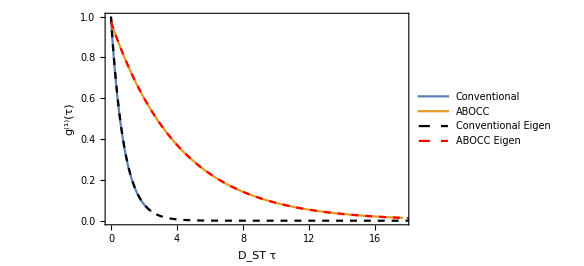

```mathematica
plt3=Show[
ListPlot[{Transpose[{gammaC/(4 nAvgC) Range[Length[record2]]100 0.025,Re[record2/nAvgC]}],Transpose[{ (Range[Length[record3]]100 0.25)/(4 nAvgA^2),Re[record3/nAvgA]}]}
,Joined->True
,PlotLegends->LineLegend[{"Conventional","ABOCC"},LabelStyle->Directive[Black,16,FontFamily->"Cambria"]]
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,ImageSize->6 72
,FrameLabel->{"D_ST τ","g^(1)(τ)"}]
,Plot[{Exp[Re[eigVal[[-2]]] t/(gammaC/(4 nAvgC))],0.97322Exp[ Re[eigValR2[[-2]]] t/(1/(4 nAvgA^2)) ]},{t,0,20},PlotStyle->{{Black,Dashed},{Red,Dashed}}
,PlotLegends->LineLegend[{"Conventional Eigen","ABOCC Eigen"},LabelStyle->Directive[Black,16,FontFamily->"Cambria"]]
,PlotRange->Full]
]
```

```mathematica
totalTime=3 45000;
freqRes=1/totalTime;
samplingRate=1/( 100 dt);
```

```mathematica
freqCoord=(-freqRes (#1-HeavisideTheta[#1-(samplingRate/(2 freqRes)+1/2)] (samplingRate/freqRes+1))&)/@Range[0,samplingRate/freqRes];
```

```mathematica
dataTime=Join[{1},Re[record3/Tr[aOpᵀ.aOp.steady]]];
```

```mathematica
aboccData = Join[{{0,1}},Transpose[{ Range[Length[record3]]100 0.25,Re[record3/nAvgA]}]];
```

```mathematica
{eigValR3,eigVectR3}=Eigensystem[superOp,-200];
```

```mathematica
eigValR3F = Select[Union[Chop[eigValR3[[100;;]]],SameTest->(Abs[#1-#2]<1.*^-6&)],#≠0&]
```

{-0.00560546,-0.00554311,-0.00524208,-0.00517772,-0.00490931,-0.00481957,-0.00460451,-0.00446978,-0.00432516,-0.00412947,-0.0040689,-0.0038335,-0.00379951,-0.00361689,-0.00348027,-0.0034171,-0.0032323,-0.00317153,-0.00306079,-0.00290095,-0.00287284,-0.00275131,-0.00261045,-0.00258488,-0.00247708,-0.00234997,-0.00231276,-0.00222798,-0.00211005,-0.00207221,-0.00199518,-0.00189597,-0.00188242,-0.00182881-2.37016×10^-10 ⅈ,-0.00177092,-0.00165985,-0.00154849,-0.00143619,-0.00132243,-0.00120682,-0.0010892,-0.000969677,-0.000848698,-0.00072714,-0.000606324,-0.000487987,-0.000374165,-0.000267082,-0.000169337,-0.0000851892,-0.0000236915}

```mathematica
c[#]&/@Range[Length[eigValR3F]]
```

{c[1],c[2],c[3],c[4],c[5],c[6],c[7],c[8],c[9],c[10],c[11],c[12],c[13],c[14],c[15],c[16],c[17],c[18],c[19],c[20],c[21],c[22],c[23],c[24],c[25],c[26],c[27],c[28],c[29],c[30],c[31],c[32],c[33],c[34],c[35],c[36],c[37],c[38],c[39],c[40],c[41],c[42],c[43],c[44],c[45],c[46],c[47],c[48],c[49],c[50],c[51]}

```mathematica
fun=Total[(c[#]&/@Range[Length[eigValR3F]]Exp[Re[eigValR3F] t])]
```

ⅇ^(-0.00560546 t) c[1]+ⅇ^(-0.00554311 t) c[2]+ⅇ^(-0.00524208 t) c[3]+ⅇ^(-0.00517772 t) c[4]+ⅇ^(-0.00490931 t) c[5]+ⅇ^(-0.00481957 t) c[6]+ⅇ^(-0.00460451 t) c[7]+ⅇ^(-0.00446978 t) c[8]+ⅇ^(-0.00432516 t) c[9]+ⅇ^(-0.00412947 t) c[10]+ⅇ^(-0.0040689 t) c[11]+ⅇ^(-0.0038335 t) c[12]+ⅇ^(-0.00379951 t) c[13]+ⅇ^(-0.00361689 t) c[14]+ⅇ^(-0.00348027 t) c[15]+ⅇ^(-0.0034171 t) c[16]+ⅇ^(-0.0032323 t) c[17]+ⅇ^(-0.00317153 t) c[18]+ⅇ^(-0.00306079 t) c[19]+ⅇ^(-0.00290095 t) c[20]+ⅇ^(-0.00287284 t) c[21]+ⅇ^(-0.00275131 t) c[22]+ⅇ^(-0.00261045 t) c[23]+ⅇ^(-0.00258488 t) c[24]+ⅇ^(-0.00247708 t) c[25]+ⅇ^(-0.00234997 t) c[26]+ⅇ^(-0.00231276 t) c[27]+ⅇ^(-0.00222798 t) c[28]+ⅇ^(-0.00211005 t) c[29]+ⅇ^(-0.00207221 t) c[30]+ⅇ^(-0.00199518 t) c[31]+ⅇ^(-0.00189597 t) c[32]+ⅇ^(-0.00188242 t) c[33]+ⅇ^(-0.00182881 t) c[34]+ⅇ^(-0.00177092 t) c[35]+ⅇ^(-0.00165985 t) c[36]+ⅇ^(-0.00154849 t) c[37]+ⅇ^(-0.00143619 t) c[38]+ⅇ^(-0.00132243 t) c[39]+ⅇ^(-0.00120682 t) c[40]+ⅇ^(-0.0010892 t) c[41]+ⅇ^(-0.000969677 t) c[42]+ⅇ^(-0.000848698 t) c[43]+ⅇ^(-0.00072714 t) c[44]+ⅇ^(-0.000606324 t) c[45]+ⅇ^(-0.000487987 t) c[46]+ⅇ^(-0.000374165 t) c[47]+ⅇ^(-0.000267082 t) c[48]+ⅇ^(-0.000169337 t) c[49]+ⅇ^(-0.0000851892 t) c[50]+ⅇ^(-0.0000236915 t) c[51]

```mathematica
r = FindFit[aboccData[[1000;;]],Flatten[{fun,Total[c[#]&/@Range[Length[eigValR3F]]]≤ 1,c[#]≥0&/@Range[Length[eigValR3F]]}],c[#]&/@Range[Length[eigValR3F]],t]
```

{c[1]→0.000512501,c[2]→0.000512501,c[3]→0.000512501,c[4]→0.000512501,c[5]→0.000512501,c[6]→0.000512501,c[7]→0.000512501,c[8]→0.000512501,c[9]→0.000512501,c[10]→0.000512501,c[11]→0.000512501,c[12]→0.000512501,c[13]→0.000512501,c[14]→0.000512501,c[15]→0.000512501,c[16]→0.000512501,c[17]→0.000512501,c[18]→0.000512501,c[19]→0.000512501,c[20]→0.000512501,c[21]→0.000512501,c[22]→0.000512501,c[23]→0.000512501,c[24]→0.000512501,c[25]→0.000512501,c[26]→0.000512501,c[27]→0.000512501,c[28]→0.000512501,c[29]→0.000512501,c[30]→0.000512501,c[31]→0.000512501,c[32]→0.000512501,c[33]→0.000512501,c[34]→0.000512501,c[35]→0.000512501,c[36]→0.000512501,c[37]→0.000512501,c[38]→0.000512501,c[39]→0.000512501,c[40]→0.000512501,c[41]→0.000512501,c[42]→0.000512501,c[43]→0.000512501,c[44]→0.000512501,c[45]→0.000512501,c[46]→0.000512498,c[47]→0.000512447,c[48]→0.00051177,c[49]→0.000508428,c[50]→0.000411313,c[51]→0.973422}

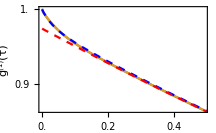

```mathematica
plt5p=Show[
ListPlot[{{#[[1]] 1/(4 nAvgA^2),#[[2]]}&/@aboccData[[;;200]],Transpose[{ (Range[Length[record3[[;;200]]]]100 0.25)/(4 nAvgA^2),Re[record3[[;;200]]/nAvgA]}]}
,Joined->True
,FrameTicks->{{{0.90,1.0},None},{{0.,0.2,0.4},None}}
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,ImageSize->3.0 72
,FrameLabel->{"D_ST τ","g^(1)(τ)"}
]
,Plot[{fun/.r/.{t->x/ (1/(4 nAvgA^2))},0.9734Exp[eigValR3F[[-1]] t]/.{t->x/(1/(4 nAvgA^2))}},{x,0,0.5},PlotStyle->{{Blue,Dashed},{Red,Dashed}}]
]
```

```mathematica
totalTime2=15 aboccData[[-1,1]];
freqRes2=1/totalTime2;
samplingRate2=1/(aboccData[[3,1]]-aboccData[[2,1]]);
```

```mathematica
freqCoord2=(-freqRes2 (#1-HeavisideTheta[#1-(samplingRate2/(2 freqRes2)+1/2)] (samplingRate2/freqRes2+1))&)/@Range[0,samplingRate2/freqRes2];
```

```mathematica
timeCoord2=Range[0,totalTime2,1/samplingRate2];
```

```mathematica
timeCoord2//Dimensions
```

{108001}

```mathematica
freqCoord2//Dimensions
```

{108001}

```mathematica
timeDataE=Transpose[{timeCoord2, fun/.r/.{t->timeCoord2}}];
timeData2E=Transpose[{timeCoord2,0.97322Exp[eigValR3F[[-1]]timeCoord2]}];
```

```mathematica
f2E=Fourier[timeDataE[[All,2]]];
f3E=Fourier[timeData2E[[All,2]]];
```

```mathematica
dt = 0.25;
```

```mathematica
record4={};
vec0 = Re[Flatten[aOp.steady]];

vecT = vec0;
tf=15 4 45000;
dt = 0.25;
step = Round[tf/dt];
Print[step]
Monitor[
Do[
k1=superOp.vecT;
k2 = superOp.(vecT+k1 dt);
vecT = vecT + 1/2(k1+k2) dt;
If[ Mod[j,100]==0,
mtx=Partition[vecT,Length[aOp]];

mtx= Partition[vecT,Length[aOp]];
AppendTo[record4,Tr[aOpᵀ.mtx]]
];
,{j,step}];
,j]
```

10800000

```mathematica
record4=record4/Tr[aOpᵀ.aOp.steady];
record4=Join[{1},record4];
```

```mathematica
Save[FileNameJoin[{saveDir,"long_time_ABOCC_record4.m"}],record4];
```

```mathematica
totalTime3=(Length[record4]-1) 100 0.25;
freqRes3=1/totalTime3;
samplingRate3=1/(100 0.25);
```

```mathematica
freqCoord3=(-freqRes3 (#1-HeavisideTheta[#1-(samplingRate3/(2 freqRes3)+1/2)] (samplingRate3/freqRes3+1))&)/@Range[0,samplingRate3/freqRes3];
```

```mathematica
f4=Fourier[Re[record4]];
```

```mathematica
Length[f4]
```

108001

```mathematica
plt6=Show[
ListPlot[Sort[Transpose[{2π freqCoord3/(1/(4 nAvgC^2)),1/1000(√Length[f4])Re[f4]}]],PlotMarkers->{Automatic,6}
,PlotRange->{{-0.0001/(1/(4 nAvgC^2)),0.0001/(1/(4 nAvgC^2))},{0,2.0 }}
,PlotLegends->LineLegend[{"Numerical Data"},LabelStyle->Directive[Black,16,FontFamily->"Cambria"]]
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,Axes->None
,GridLines->{{{eigValR3F[[-1]]/(1/(4 nAvgC^2)),Directive[Black,Dashed,Opacity[1]]},{-eigValR3F[[-1]]/(1/(4 nAvgC^2)),Directive[Black,Dashed,Opacity[1]]}},None}
,FrameLabel->{"ω/D_ST","ℱ[g^(1)] (arb. unit)"}
,PlotLegends->LineLegend[{"Fit, 20 Eigenvalues","Single Eigenvalue"},LabelStyle->Directive[Black,16,FontFamily->"Cambria"]]
,ImageSize->6 72
],
ListPlot[{Sort[Transpose[{2π freqCoord2/(1/(4 nAvgC^2)),1/1000(√Length[f2E])Re[f2E]}]],Sort[Transpose[{ 2π freqCoord2/(1/(4 nAvgC^2)),1/1000(√Length[f3E])Re[f3E]}]]}

,PlotRange->{{-0.0001/(1/(4 nAvgC^2)),0.0001/(1/(4 nAvgC^2))},{0,2.0 }}
,PlotStyle->{ColorData[97][2],ColorData[97][3]}
,Joined->True
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,Axes->None
,GridLines->{{{eigValR3F[[-1]]/(1/(4 nAvgC^2)),Directive[Black,Dashed,Opacity[1]]},{-eigValR3F[[-1]]/(1/(4 nAvgC^2)),Directive[Black,Dashed,Opacity[1]]}},None}
,FrameLabel->{"ω/D_ST","ℱ[g^(1)] (arb. unit)"}
,PlotLegends->LineLegend[{"Fit, 51 Eigenvalues","Single Eigenvalue"},LabelStyle->Directive[Black,16,FontFamily->"Cambria"]]
,ImageSize->6 72
]
]
```

-Graphics-

```mathematica
plotDataNum = Sort[Transpose[{2π freqCoord3/(1/(4 nAvgC^2)),1/1000(√Length[f4])Re[f4]}]];
plotDataFt51=Sort[Transpose[{2π freqCoord2/(1/(4 nAvgC^2)),1/1000(√Length[f2E])Re[f2E]}]];
plotDataFtSingle=Sort[Transpose[{ 2π freqCoord2/(1/(4 nAvgC^2)),1/1000(√Length[f3E])Re[f3E]}]];
```

```mathematica
plt6NumZoom = Select[plotDataNum,2>#[[1]]>1.5&];
plt6Ft51Zoom = Select[plotDataFt51,2>#[[1]]>1.5&];
plt6FitSingleZoom = Select[plotDataFtSingle,2>#[[1]]>1.5&];
```

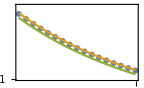

```mathematica
plt6zoom=Show[
ListPlot[plt6NumZoom[[;;;;2]],PlotMarkers->{Automatic,6}
,PlotRange->{{1.5,2.0},{0.01,0.02}}
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,Axes->None
,GridLines->{{{eigValR3F[[-1]]/(1/(4 nAvgC^2)),Directive[Black,Dashed,Opacity[1]]},{-eigValR3F[[-1]]/(1/(4 nAvgC^2)),Directive[Black,Dashed,Opacity[1]]}},None}
,FrameTicks->{{{0.01,0.02,0.04},None},{{1.0,1.5,2.0},None}}
,ImageSize->2 72
],
ListPlot[{plt6Ft51Zoom,plt6FitSingleZoom}
,PlotRange->{{-0.0001/(1/(4 nAvgC^2)),0.0001/(1/(4 nAvgC^2))},{0,2.0 }}
,PlotStyle->{ColorData[97][2],ColorData[97][3]}
,Joined->True
,Frame->True,FrameStyle->Directive[Black,FontSize->16,FontFamily->"Cambria"]
,Axes->None
,GridLines->{{{eigValR3F[[-1]]/(1/(4 nAvgC^2)),Directive[Black,Dashed,Opacity[1]]},{-eigValR3F[[-1]]/(1/(4 nAvgC^2)),Directive[Black,Dashed,Opacity[1]]}},None}
,FrameLabel->{"ω/D_ST","ℱ[g^(1)] (arb. unit)"}
]
]
```